ExampleData::obsolete: {TestImage,Lena} is being deprecated, and may not be available in future versions of the Wolfram Language.

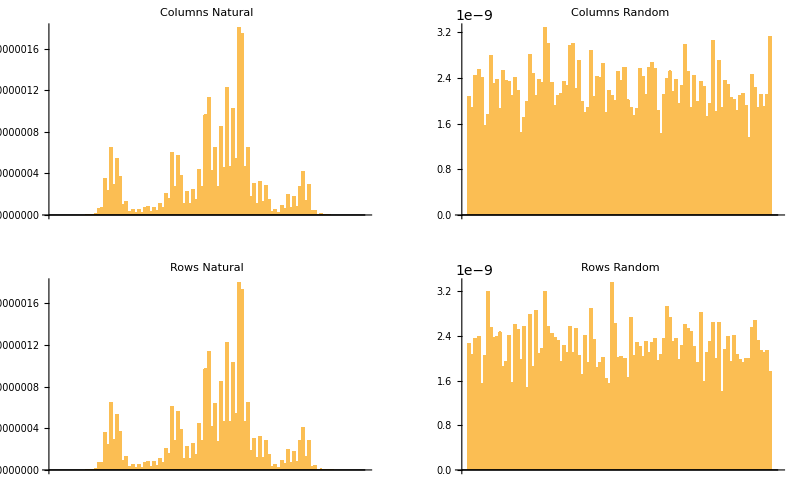

```mathematica
imgN=ExampleData[{"TestImage","Lena"}];
imgR = imgR=RandomImage[];
matN=ImageCooccurrence[imgN,100];
matR = ImageCooccurrence[imgR,100];
GraphicsGrid[{
{BarChart[Variance[matN], PlotLabel->"Columns Natural"], BarChart[Variance[matR], PlotLabel->"Columns Random"]}, {BarChart[Variance/@matN, PlotLabel->"Rows Natural"], BarChart[Variance/@matR, PlotLabel->"Rows Random"]}
}]
```

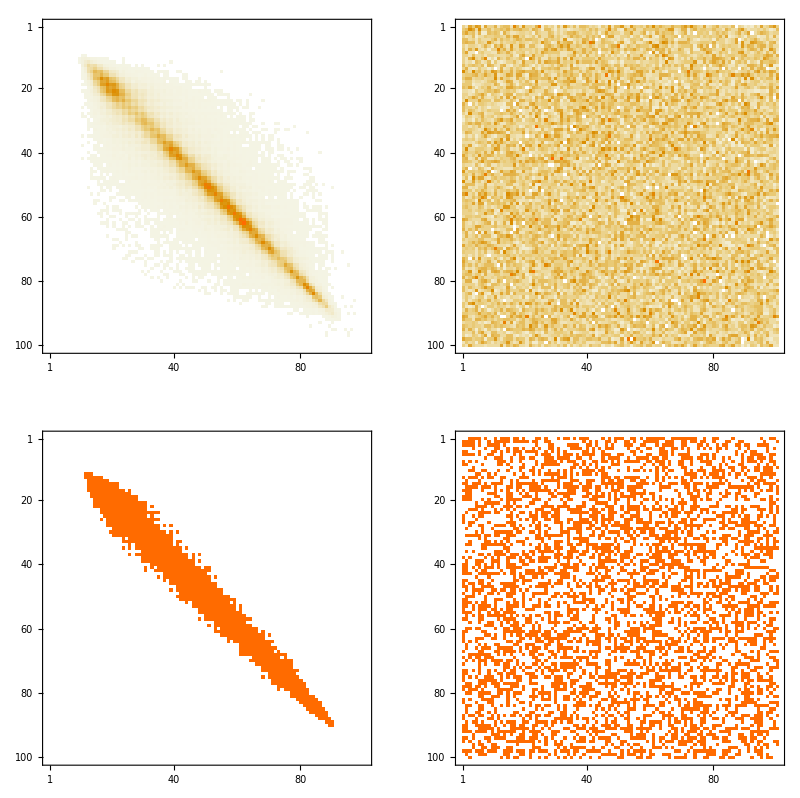

```mathematica
threshold = 0.0001;
binmatN = Clip[matN,{threshold, threshold},{0,1}];
binmatR = Clip[matR,{threshold, threshold},{0,1}];
GraphicsGrid[{{MatrixPlot[matN], MatrixPlot[matR]},
{MatrixPlot[binmatN], MatrixPlot[binmatR]}}]
```

```mathematica
idxs = {idxN = Position[binmatN, 1], idxR = Position[binmatR, 1]};
N[Variance[#]]&/@ idxs
```

{{396.266,398.472},{841.381,847.016}}

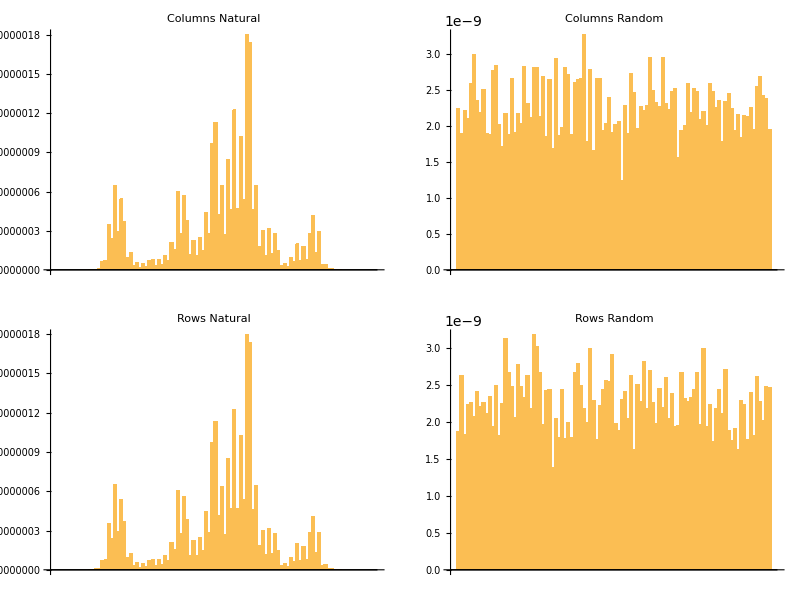

```mathematica
TableForm@{
{BarChart[Variance[matN], PlotLabel->"Columns Natural"], BarChart[Variance[matR], PlotLabel->"Columns Random"]}, {BarChart[Variance/@matN, PlotLabel->"Rows Natural"], BarChart[Variance/@matR, PlotLabel->"Rows Random"]}
}
```